```mathematica
(*** Soliton ***)
    * Solitons are the solution of non-linear dispersive partial differential equations.
* They are localized within a region.
* They Collide with other solitons and remain unchanged in shape.
* They retained their speed after interaction with other solitons.
```

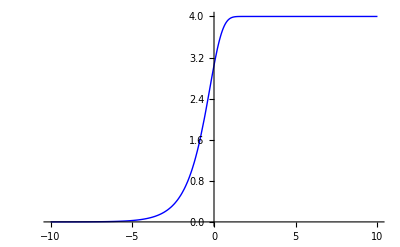

```mathematica
Pulse Soliton (due to +ve Sign);
t=0;
Plot[(4 Tanh[Exp[x  +t]]),{x,-10,10},PlotStyle->{{Blue,Thick}},PlotRange->All]
```

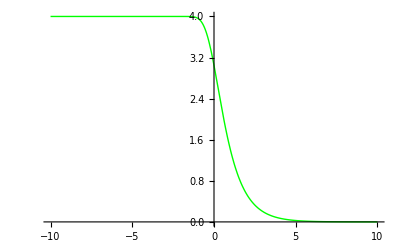

```mathematica
Dark Soliton (due to -ve Sign);
Plot[(4 Tanh[Exp[-x  +t]]),{x,-10,10},PlotStyle->{{Green,Thick}},PlotRange->All]
```

```mathematica
Animation of Pulse Soliton and Kink Soliton  Together;
```

```mathematica
Animate[Plot[( -4 Tanh[Exp[-x  +t]]-4 Tanh[Exp[x  +t]]),{x,-10,10},PlotStyle->{{Red,Thick}},PlotRange->All],{t,-0.1,10}]
```